```mathematica
out = ;
```

```mathematica
outa =Association[ParallelMap[#[[1]]->#[[2]]&, out]];
```

```mathematica
funcassoc = Select[outa, #!=-Infinity&];
```

```mathematica
Length[funcassoc]
```

20874

### Attempt 1

```mathematica
20000^2
```

400000000

```mathematica
mutemat = Module[{digs},
ParallelTable[
digs = IntegerDigits[functional[[i, 1]],  4, 4^3];
Boole[Count[Unitize[digs - IntegerDigits[functional[[j, 1]],  4, 4^3]], 1]==1],
{i, 1, Length[functional[[;;100]]] - 1}, {j, i + 1, Length[functional[[;;100]]]}]];
```

```mathematica
functional = Select[out, #[[2]]!=-Infinity&];
```

```mathematica
Length[functional]
```

20874

```mathematica
HammingDistance[{1, 2, 3, 2}, {1, 2, 3, 2}]
```

0

```mathematica
ParallelDo[]
```

```mathematica
results = Module[{digs, results = {}},SetSharedVariable[results];
 ParallelDo[
digs = IntegerDigits[functional[[i, 1]],  4, 4^3];
If[HammingDistance[digs, IntegerDigits[functional[[j, 1]],  4, 4^3]] ==1, AppendTo[results, {i, j}]],
{i, 1, Length[functional[[;;1000]]] - 1}, {j, i + 1, Length[functional[[;;1000]]]}];
results
];
```

$Aborted

```mathematica
ByteCount[results]*(2000^2)
```

94432000000

```mathematica
100^2
```

10000

```mathematica
RandomGraph[{200000, 400000}]
```

```mathematica
ByteCount[RandomGraph[{200000, 400000}]]
```

8000592

```mathematica
results
```

```mathematica
Module[{results={}},SetSharedVariable[results];ParallelTable[If[Do[If[CellularAutomaton[{3rn,3},{Append[Table[1,n],2],0},{{{200}}}]=!=Table[1,2n+2],Return[Nothing]],{n,10}]===Null,AppendTo[results,3rn]],{rn,1503429766308-10^6,1503429766308+10^6}];results]//AbsoluteTiming
```

```mathematica
Module[{gk2r2,embedding},
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
SeedRandom[12345];
embedding=Map[#+RandomReal[20,2]&,
GraphEmbedding[gk2r2]];
Graph[gk2r2,EdgeStyle->Directive[Hue[0.6,0.4,0.5,.6],Opacity[.15]],
VertexStyle->GrayLevel[.3],VertexCoordinates->embedding]
]
```

```mathematica
Module[{gk2r2,embedding},
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
SeedRandom[12345];
embedding=Map[#+RandomReal[20,2]&,
GraphEmbedding[gk2r2]];
{{"[◼]", "addVertexFigures"}}[Graph[gk2r2,
EdgeStyle->Directive[Hue[0.6,0.4,0.5,.6],Opacity[.15]],
VertexStyle->Gray,VertexCoordinates->embedding],
{{"[◼]", "$LifetimeData"}}[2,2,"All"],
{{"[◼]", "changeFitness"}}[{2,2},
{{"[◼]", "$LifetimeData"}}[2,2,"All"],
Length@*First],
VertexSize->1.5]
]
```

```mathematica
co   = Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]];
```

```mathematica
ByteCount[co]
```

1883112

```mathematica
HighlightGraph[#,Style[VertexList[#][[1]],Red,PointSize[.015]]]&@Graph[WeaklyConnectedGraphComponents[
Once@Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]],EdgeStyle->Directive[Directive[{Hue[0.6,0.4,0.5,.6]}],Opacity[.15]],
VertexStyle->GrayLevel[.3],GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{"[◼]", "addVertexFigures"}}[VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
GraphLayout->"LayeredDigraphEmbedding",
"Reduced"->True,
AspectRatio->.7,
EdgeStyle->Directive[{Hue[0.6,0.4,0.5,.6]}]
],{{0,65815}}],{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},
"VertexFigures"->1,VertexSize->.3]
```

### Attempt 2

```mathematica
mr = {216669022433126270203581211982533285004,4,1};
```

```mathematica
mr1 = mr[[1]];
```

```mathematica
FromDigits[#, 4]&/@(Tuples[(MapAt[Range[0, 3]&,List/@ IntegerDigits[mr[[1]],4, 4^3] ,List/@Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]])]);
```

```mathematica
List/@Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]
```

{{1},{5},{9},{17},{21},{25},{33},{37},{41}}

```mathematica
(MapAt[Range[0, 3]&,List/@ IntegerDigits[mr[[1]],4, 4^3] ,List/@Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]]])
```

{{0,1,2,3},{2},{0},{3},{0,1,2,3},{0},{0},{0},{0,1,2,3},{2},{3},{3},{2},{1},{0},{2},{0,1,2,3},{3},{2},{0},{0,1,2,3},{1},{2},{3},{0,1,2,3},{1},{1},{1},{0},{3},{3},{0},{0,1,2,3},{2},{2},{2},{0,1,2,3},{0},{3},{2},{0,1,2,3},{1},{3},{1},{0},{1},{2},{3},{2},{2},{3},{1},{0},{2},{1},{0},{3},{1},{1},{0},{2},{0},{3},{0}}

```mathematica
NestGraph[IntegerDigits[mr[[1]], 4, 4^3], ]
```

### Other ideas

What if I get the intersection of the mutation generations at each step or something. I mean there’s basically 200,000,000 potential connections between viable nodes. We just want to see where there are nodes that are only connected to nodes with lower fitness. Then we can start enumerating the potential

```mathematica
20000*30
```

600000

```mathematica
idxs = Select[{{"[◼]", "RuleTuples"}}[4, 1], Count[#, 0]==0&->"Index"][[1;;All;;3]];
```

```mathematica
functional[[1]]
```

{46523944710399056089392556413439759500,14}

```mathematica
functional[[;;10]]
```

{{46523944710399056089392556413439759500,14},{46523944710399056089392697150928114828,26},{46523944710399056089410641180693419148,51},{46523944710399056089428585210458723468,18},{46523944710399056089446669977712383116,30},{46523944710399056094004242431867147404,14},{46523944710399056094004312800611325068,37},{46523944710399056094004383169355502732,26},{46523944710399056094022327199120807052,52},{46523944710399056094040271228886111372,18}}

```mathematica
(getallpointmutations[{#[[1]], 4, 1}, idxs]&/@ functional[[;;10000]])
```

```mathematica
funcassoc[[;;1]]
```

<|46523944710399056089392556413439759500→14|>

```mathematica
allviablemutations = (getallpointmutations[{#[[1]], 4, 1}, idxs]&/@ functional);
```

```mathematica
allmutations = ParallelMap[getallpointmutations[{#[[1]], 4, 1}, idxs]&, out];
```

```mathematica
ByteCount[allmutations]
```

634391160

```mathematica
peaks = Pick[functional, MapThread[Function[{rule, mutations}, AllTrue[DeleteMissing[Lookup[funcassoc, mutations]], #<= rule[[2]]&]], {functional, allviablemutations}]];
```

```mathematica
allpeaks = Pick[out, MapThread[Function[{rule, mutations}, AllTrue[DeleteMissing[Lookup[outa, mutations]], #<= rule[[2]]&]], {out, allmutations}]];
```

```mathematica
peaks = MapThread[Function[{rule, mutations}, AllTrue[Echo[DeleteMissing[Lookup[funcassoc, mutations]]], #<= rule[[2]]&]], {functional[[;;1]], allviablemutations[[;;1]]}];
```

```mathematica
Position[peaks, True]
```

{}

```mathematica
Length[peaks]
```

0

```mathematica
Length[peaks]
```

11372

```mathematica
gps = GroupBy[peaks, Last];
```

```mathematica
allgps = GroupBy[allpeaks, Last];
```

```mathematica
Length[allgps]
```

367

```mathematica
Length[gps]
```

366

```mathematica
Log[0]
```

-∞

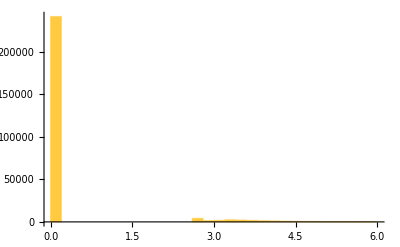

```mathematica
Histogram[Log/@(outa/.-Infinity->1), PlotRange->All]
```

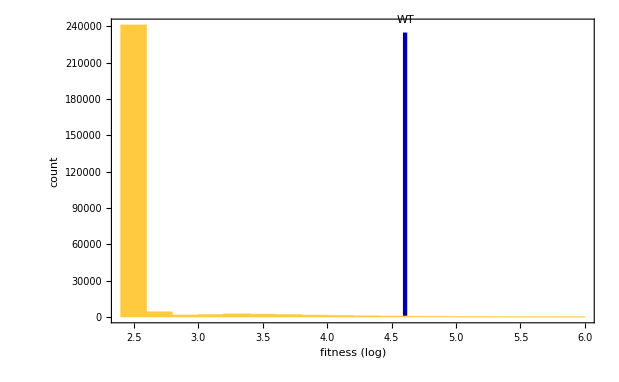

```mathematica
Histogram[Log/@(outa/.-Infinity->12.5), PlotRange->All, Epilog->{Style[Text["WT", {Log[100], 245000}],13],Thickness[.005],Darker[Blue],  Line[{{Log[100], 1000}, {Log[100], 235000}}]}, Frame->True, FrameLabel->{"fitness (log)", "count"}]
```

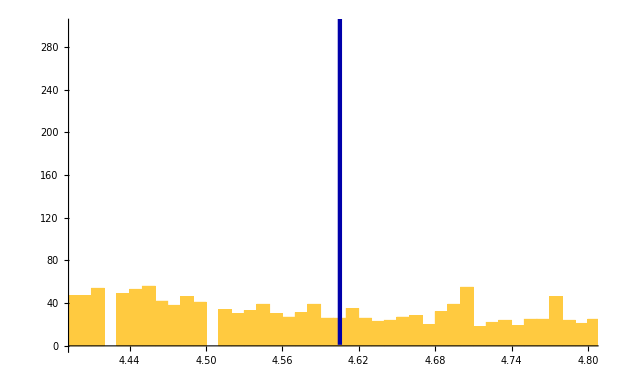

```mathematica
Histogram[Log/@(outa/.-Infinity->12.5),  {.01},Epilog->{Style[Text["WT", {Log[100], 245000}],13],Thickness[.005],Darker[Blue], Line[{{Log[100], 1}, {Log[100], 235000}}]}, PlotRange->{{4.4, 4.8}, {0, 300}}]
```

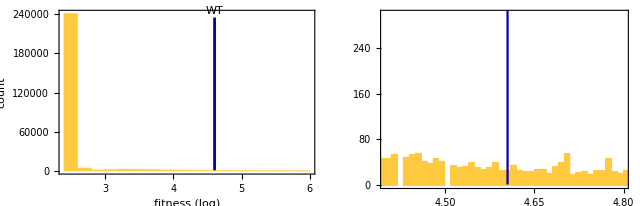

```mathematica
GraphicsRow[{, Show[, ImageSize->320, Frame->True, PlotRangeClipping->True]}]
```

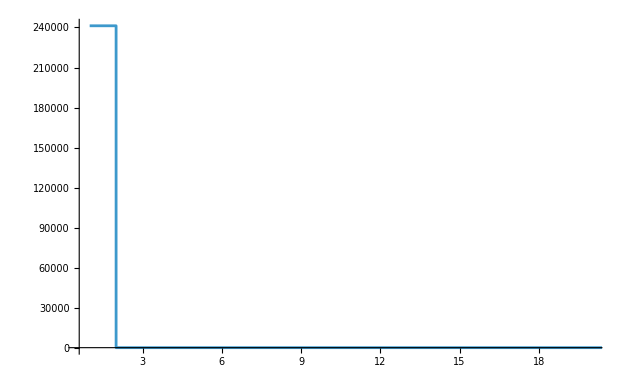

```mathematica
ListStepPlot[BinCounts[Values[Log/@(outa/.-Infinity->1)], {0, 2, .1}], PlotRange->All]
```

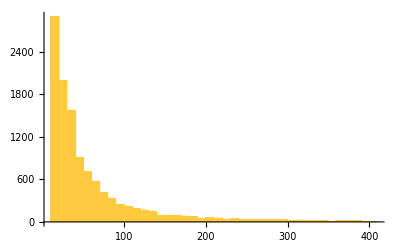

```mathematica
Histogram[peaks[[All, 2]], PlotRange->All]
```

```mathematica
Histogram[allpeaks[[All, 2]], PlotRange->All]
```

-Graphics-

```mathematica
TestCALifetime[CellularAutomaton[mr, {{1}, 0}, 200]]
```

100

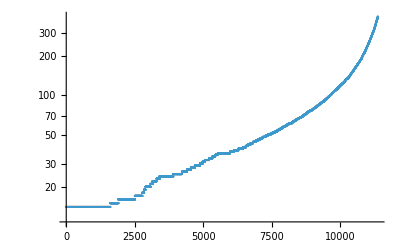

```mathematica
ListPlot[Sort[peaks[[All, -1]]], PlotRange->All, ScalingFunctions->"Log"]
```

```mathematica
Outer[f, {1, 2, 3}, {4, 5, 6}]
```

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

Run this overnight

```mathematica
pds =
Module[{ups = Values[gps[[All, 1]]], digs},
 ParallelTable[
digs = IntegerDigits[ups[[i, 1]],  4, 4^3];
HammingDistance[digs , IntegerDigits[ups[[j, 1]],  4, 4^3]],
{i, 1, Length[ups] - 1}, {j, i + 1, Length[ups]}]];
```

```mathematica
Iconize[pds]
```

Genetic distance between peaks:

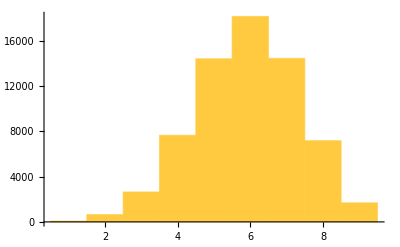

```mathematica
Histogram[Catenate[pds]]
```

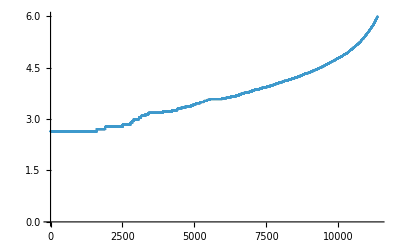

```mathematica
ListPlot[Log/@Sort[allpeaks[[All, -1]]], PlotRange->All]
```

```mathematica
Lighter[Orange]
```

```mathematica
RGBColor[1, 0.6666666666666666, 0.41000000000000003]
```

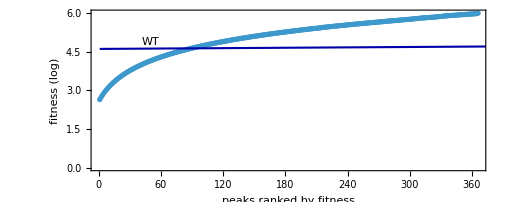

```mathematica
ListPlot[Log/@Sort[Keys[gps[[All, 1]]]], PlotRange->All, Epilog->{Style[Text["WT", Reverse@{Log[100] + .25, 50}],13],Thickness[.003],Darker[Blue], Line[{ Reverse@{Log[100], 1}, Reverse@{Log[100] +.1 , 400}}]}, Frame->True, FrameLabel->{"peaks ranked by fitness", "fitness (log)"}, AspectRatio->.4]
```

TODO: Reach out to Andreas Wagner and figure out what the hell their scaling function for fitness is. Also need to compare their data with other data.

```mathematica
Length[out]
```

262144

```mathematica
Length[peaks]
```

11372

```mathematica
Length[functional]
```

20874

```mathematica
Length[gps]
```

366